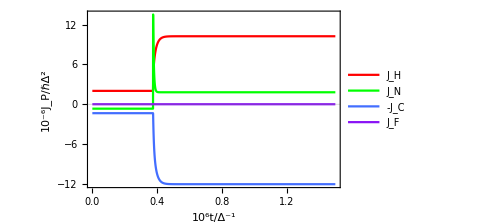
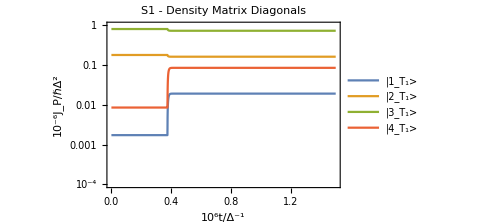
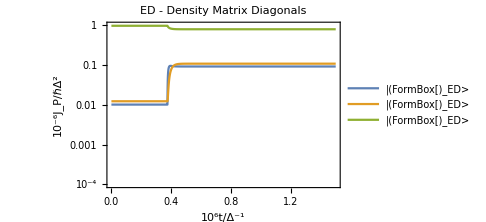
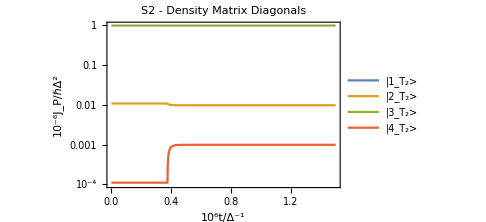

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2,ωED,γT1s,γT2s, Tcnt1,Tcnt2,tstart,tchange,tmax},
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω1=0ωconv;Ω2=0ωconv;
ωED=0.2ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Tcnt1=0.05Tconv;Tcnt2=0.2Tconv;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=0tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2,ωED,γT1s,γT2s, Tcnt1,Tcnt2,tstart,tchange,tmax]
]
```

```mathematica
X=-Graphics-;
Show[X]
```

-Graphics-

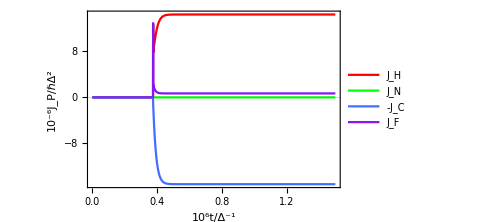
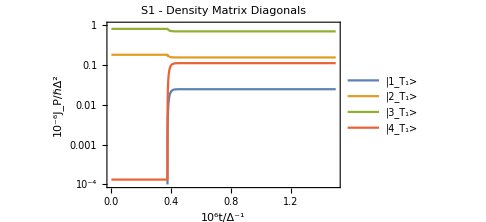
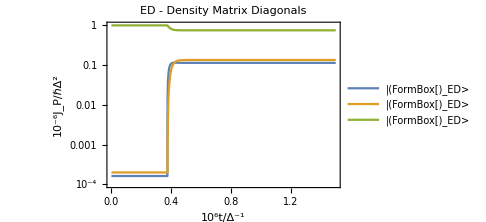
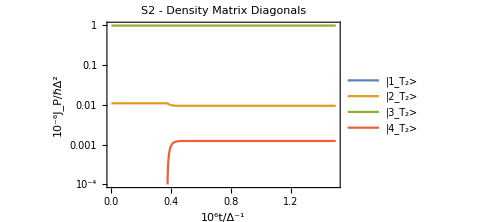

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol, ωLM1,ωMR1,ωLM2,ωMR2,Ω2,ωED,γT1,γT2, Ωcnt1,Ωcnt2,tstart,tchange,tmax},
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω2=0ωconv;
ωED=0.2ωconv;γT1=0.015ωconv;γT2=0.015ωconv;
Ωcnt1=0.01ωconv*κhot;Ωcnt2=0.5ωconv*κhot;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=0tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, ωED,γT1,γT2,Ωcnt1,Ωcnt2,tstart,tchange,tmax]
]
```

```mathematica
kB ((ℏ ω)/(kB T))^2 ⅇ^((ℏ ω)/(kB T))/((ⅇ^((ℏ ω)/(kB T))-1)^2)/.{ℏ->1,kB->1,ω->0.2,T->0.2}
∑_(k=0)^n (kB ((ℏ Subscript[ω, k])/(kB T))^2 ⅇ^((ℏ Subscript[ω, k])/(kB T))/((ⅇ^((ℏ Subscript[ω, k])/(kB T))-1)^2))//.{ℏ->1,kB->1,Subscript[ω, k_]->ωmin+(ωmax-ωmin)/n k,ωmin->0.025,ωmax->0.25,n->50,T->0.2}
```

0.920674

48.6381

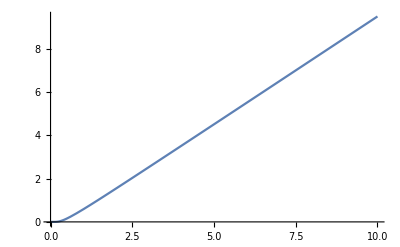

```mathematica
Plot[1/(ⅇ^(1/T)-1),{T,0,10}]
```

### Time domain behaviors

```mathematica
findInitMatrix[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1_,Ω2_,γT1s_,γT2s_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[κ, 3]->κ3,Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,ωED->ωEDs,Table[γT1[i]->γT1s,{i,0,Ns-1-p}],Table[γT2[i]->γT2s,{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NSolve[Flatten[{temp1//.{Subscript[ρ, i_,j_]'[t]->0,Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j]},∑_(i=1)^(16 Ns) Subscript[ρ, i,i]==1}],Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]]];
temp3=Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]//.Flatten[temp2];
Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]/.temp2
]
```

```mathematica
PlotTimeDomainWithΩ[Thots_,Tcnts_,Tcols_,κhots_,κcnts_,κcols_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω2_,ωEDs_,γT1s_,γT2s_, Ωcnt1s_,Ωcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,initMatrix,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS1graph,denmatS2graph,denmatEDgraph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Ωcnt-> Piecewise[{{Ωcnt1s,t<tchange},{Ωcnt2s,t>tchange}}]
};
sysassum = {
Subscript[T, 1]-> Thots,Subscript[T, 2]-> Tcnts,Subscript[T, 3]-> Tcols,
Subscript[κ, 1]->κhots,Subscript[κ, 2]->κcnts,Subscript[κ, 3]->κcols,
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ωcnt,Subscript[Ω, 2]->Ω2,
ωED->ωEDs,
γT1[i_]->γT1s,γT2[i_]->γT2s
};

initMatrix=findInitMatrix[Thots,Tcnts,Tcols,κhots,κcnts,κcols,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ωcnt1s,Ω2,γT1s,γT2s,unitassum];

motioneqs=sol//.Flatten[{NBEassum,unitassum,timeassum,sysassum,Jassum}];
initconditions={Table[Subscript[ρ, i,j][0]==initMatrix[[1,i,j]],{i,1,16Ns},{j,1,16Ns}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,tstart,tmax}
];

denmatS1graph=Flatten[Table[PartialTraceT1[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,4}]/.dynamics];
denmatEDgraph=Flatten[Table[PartialTraceED[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,Ns}]/.dynamics];
denmatS2graph=Flatten[Table[PartialTraceT2[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,4}]/.dynamics];

flowgraph=Re[Flatten[10^6{
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]],
Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],
Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]]}//.Flatten[{NBEassum,unitassum,timeassum,sysassum,Jassum}]/.dynamics]]/.t->10^6 t;

{
timedom=Plot[flowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic, Automatic},
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotStyle->{Red,Green,BlueC,PurpleC}],
LogPlot[denmatS1graph,{t,0,10^-6 tmax},
ImageSize->Medium,
	PlotLabel->  Style["S1 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}
],
LogPlot[denmatEDgraph,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["ED - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->Table[Style[StringForm["|(``)_ED>",Ns-i],FontFamily->"Times New Roman",FontSize->14.5],{i,1,Ns}]
],
LogPlot[denmatS2graph,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["S2 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
]
}
]
```